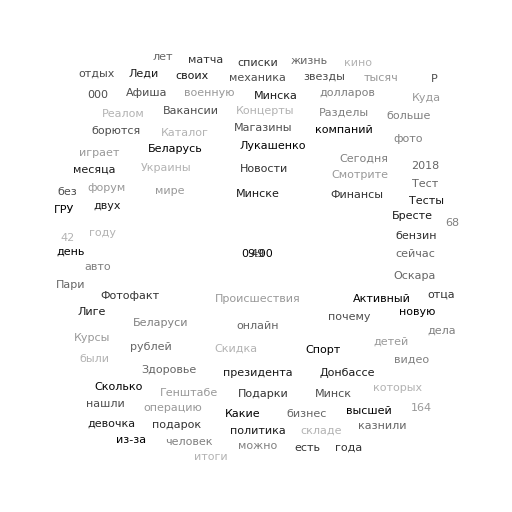

```mathematica
stopwords={"в","и","а","на","до","по","c","к","о","но","как","под","за","про","над","я","где","не","с","это","из","об","при","чего","или","что","все","от","км","руб","да","нет","1","2","3","4","5","6","7","8","9","0","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25","26","27","28","29","30","31" "у","ещё","кто","был","свернуть","оставить","поделиться","комментарий","вот","того","всю","там","еще","их","для","метки","ты","вы","бы","ее","же","так","in","то","уже","account","этом","этот","оно","она","они","чем","раз","то","он","create","два","log","либо","себе","свою","нас","комментариев","вашей","эта","тоже","тут","меня","две","сам","себя","мы","этого","моя","со","тоже","этого","его","мне","наша","вас","эту","тех","вам","мои","у","этим","январь","января","февраль","февраля","март","марта","апрель","апреля","май","мая","июнь","июня","июль","июля","август","августа","сентябрь","сентрября","октябрь","октября","ноябрь","ноября"l,"декабрь","декабря","тебе","комментария","свой","100","том","an","english","no","login","am","этих","ну","ни","en","д","п","share","comment","comments","entries","во","tags","pm","leave","recent","the","б","ь","ъ","те","ru","рл","аз","еры","х","г","ер","february","ерь","(и,","journal","пр","a","previous","ы","сих","х","назад","ох","л","ли","ск","ей","нам"};
wordsFromSite =TextWords[Import["https://www.tut.by"]];
filteredWords =Select[wordsFromSite,!MemberQ[ToLowerCase/@stopwords,ToLowerCase[#]]&];

WordCloud[filteredWords,PlotTheme->"Monochrome",ImageSize->512]
```